```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];
<<EpidCRN`;<<red`;
(*Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
Format[mu1]:=Subscript[μ,1];Format[mu2]:=Subscript[μ,2];Format[mu3]:=Subscript[μ,3];Format[mu0]:=Subscript[μ,0];
Format[R1]:=Subscript[R,1];Format[R2]:=Subscript[R,2];Format[R3]:=Subscript[R,3];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];Format[s0]:=Subscript[s,0];
Format[th]:=θ;
Format[La]:=Λ;
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[i12]:=Subscript[i,12];*)

(*cLog={be1->0,be2->0,ga1->0,ga2->0,b->r*s*(1-s/s0),mu0->0};

cet={et1->s13 mu1 mu3 (R1-R3)/((s0-s13)mu0 s0),
et2->s23 mu2 mu3 (R2-R3)/((s0-s23)mu0 s0)};
cb=b->r*s*(1-s/s0);*)

(*Two-Strain Coinfection Model with Logistic Growth*)
cbg={be1->0,be2->0,ga1->0,ga2->0};
cbe={be1->0,be2->0};cb={b->s0 mu0};cga={ga1->0,ga2->0};
cmu={mu2 ->mu,mu3->mu,mu1 ->mu,mu0->mu};
c3={i12->0};c2={i2->0};c1={i1->0};
RHS={-be1 i12 s-be2 i12 s-mu0 s-(i1 mu1 R1 s)/s0-(i2 mu2 R2 s)/s0-(i12 mu3 R3 s)/s0+mu0 s0,-et1 i1 i12-ga1 i1 i2-i1 mu1+be1 i12 s+(i1 mu1 R1 s)/s0,-ga2 i1 i2-et2 i12 i2-i2 mu2+be2 i12 s+(i2 mu2 R2 s)/s0,et1 i1 i12+ga1 i1 i2+ga2 i1 i2+et2 i12 i2-i12 mu3+(i12 mu3 R3 s)/s0};var={s,i1,i2,i12};
{RN,rts,spe,alp,bet,gam}=ODE2RN[RHS,var];
RHS-gam.rts//FullSimplify  (*Should be {0,0,0,0}*)
mSib = minSiph[spe, (RN/.cbe)][[1]];
mSig = minSiph[spe, (RN/.cbg)][[1]];
Print["minSiph=", mSib,mSig];
```

14 reactions and rts=(0→s | mu0 s0
i12+s→i1+i12 | be1 i12 s
i1+s→2 i1 | (i1 mu1 R1 s)/s0
i12+s→i12+i2 | be2 i12 s
i2+s→2 i2 | (i2 mu2 R2 s)/s0
i1+i12→2 i12 | et1 i1 i12
i1+i2→i12+i2 | ga1 i1 i2
i1+i2→i1+i12 | ga2 i1 i2
i12+i2→2 i12 | et2 i12 i2
i12+s→2 i12 | (i12 mu3 R3 s)/s0
s→0 | mu0 s
i1→0 | i1 mu1
i2→0 | i2 mu2
i12→0 | i12 mu3)({}→{s} | mu0 s0
{s}→^{i12}{i1} | be1 i12 s
{s}→^{i1}{i1} | (i1 mu1 R1 s)/s0
{s}→^{i12}{i2} | be2 i12 s
{s}→^{i2}{i2} | (i2 mu2 R2 s)/s0
{i1}→^{i12}{i12} | et1 i1 i12
{i1}→^{i2}{i12} | ga1 i1 i2
{i2}→^{i1}{i12} | ga2 i1 i2
{i2}→^{i12}{i12} | et2 i12 i2
{s}→^{i12}{i12} | (i12 mu3 R3 s)/s0
{s}→{} | mu0 s
{i1}→{} | i1 mu1
{i2}→{} | i2 mu2
{i12}→{} | i12 mu3)

Set::shape: Lists {RN,rts,spe,alp,bet,gam} and {{0→s,i12+s→i1+i12,i1+s→2 i1,i12+s→i12+i2,i2+s→2 i2,i1+i12→2 i12,i1+i2→i12+i2,i1+i2→i1+i12,i12+i2→2 i12,i12+s→2 i12,«4»},{mu0 s0,be1 i12 s,«8»,«4»},«3»,{«1»},{{}→{s},{,{,{,«3»,{,{,{,«4»}} are not the same shape.

{-(((be1+be2) i12+mu0) s)-((i1 mu1 R1+i2 mu2 R2+i12 mu3 R3) s)/s0+mu0 s0-gam.rts,-i1 (et1 i12+ga1 i2+mu1)+be1 i12 s+(i1 mu1 R1 s)/s0-gam.rts,-i2 (ga2 i1+et2 i12+mu2)+be2 i12 s+(i2 mu2 R2 s)/s0-gam.rts,et1 i1 i12+ga1 i1 i2+ga2 i1 i2+et2 i12 i2-i12 mu3+(i12 mu3 R3 s)/s0-gam.rts}

Subsets::normal: Nonatomic expression expected at position 1 in Subsets[spe,{1,0}].

Subsets::argb: Subsets called with 0 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of Subsets::argb will be suppressed during this calculation.

Subsets::normal: Nonatomic expression expected at position 1 in Subsets[spe,{1,0}].

Subsets::argb: Subsets called with 0 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of Subsets::argb will be suppressed during this calculation.

minSiph=Subsets[]Subsets[]

{0,0,0,0}

minSiph={{i1,i12},{i2,i12}}{{i1,i12},{i2,i12}}

14 reactions and transitions: (0→s | mu0 s0
i12+s→i1+i12 | be1 i12 s
i1+s→2 i1 | (i1 mu1 R1 s)/s0
i12+s→i12+i2 | be2 i12 s
i2+s→2 i2 | (i2 mu2 R2 s)/s0
i1+i12→2 i12 | et1 i1 i12
i1+i2→i12+i2 | ga1 i1 i2
i1+i2→i1+i12 | ga2 i1 i2
i12+i2→2 i12 | et2 i12 i2
i12+s→2 i12 | (i12 mu3 R3 s)/s0
s→0 | mu0 s
i1→0 | i1 mu1
i2→0 | i2 mu2
i12→0 | i12 mu3)

RHS=(-(((be1+be2) i12+mu0) s)-((i1 mu1 R1+i2 mu2 R2+i12 mu3 R3) s)/s0+mu0 s0
-i1 (et1 i12+ga1 i2+mu1)+be1 i12 s+(i1 mu1 R1 s)/s0
-i2 (ga2 i1+et2 i12+mu2)+be2 i12 s+(i2 mu2 R2 s)/s0
et1 i1 i12+ga1 i1 i2+ga2 i1 i2+et2 i12 i2-i12 mu3+(i12 mu3 R3 s)/s0) siphons are{{i1,i12},{i2,i12}}((R1 s)/s0 | (be1 s)/mu3 | 0
0 | (R3 s)/s0 | 0
0 | (be2 s)/mu3 | (R2 s)/s0)

reduced models are{{s},{i1},{i2},{i12}}

Minimal siphons: {T_1→{i1,i12},T_2→{i2,i12}}

IGMS edges: {1->2,2->1}

Cycles found: 1

Cycles: {{1->2,2->1}}

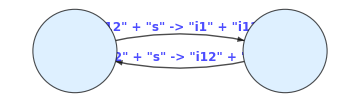

{{i12},{i1},{i2}}

```mathematica
{RHS,var,par,cp,mSi,Jx,Jy,cDFE,E0,K,R0A,infVars,ng}=NGMRN[RN,rts,var];
Print[RN//Length, " reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
Print["RHS=",RHS//FullSimplify//MatrixForm, " siphons are",mSi,K//MatrixForm];
(* MAXIMAL ELIMINABLE SETS *)
{maxId, maxSets} = maxElim[RN, rts, var];
Print["reduced models are",maxSets];
{edg,elab,cyc,graph}=IGMS[RN, mSi];
{co,nc}=findCores[RN,3];co
```

10reactions and transitions: (0→s | mu0 s0
i1+s→2 i1 | (i1 mu1 R1 s)/s0
i2+s→2 i2 | (i2 mu2 R2 s)/s0
i12+s→2 i12 | (i12 mu3 R3 s)/s0
i1+i12→2 i12 | et1 i1 i12
i12+i2→2 i12 | et2 i12 i2
s→0 | mu0 s
i1→0 | i1 mu1
i2→0 | i2 mu2
i12→0 | i12 mu3)

RHS=(-(i1 mu1 R1 s+i2 mu2 R2 s+i12 mu3 R3 s+mu0 s s0-mu0 s0^2)/s0
-i1 (et1 i12+mu1)+(i1 mu1 R1 s)/s0
-i2 (et2 i12+mu2)+(i2 mu2 R2 s)/s0
i12 (et1 i1+et2 i2+mu3 (-1+(R3 s)/s0)))mSi={{i1},{i2},{i12}}

al,be arealbe  DFE is{s→s0,i1→0,i12→0,i2→0} repr. functions  {(R1 s)/s0,(R2 s)/s0,(R3 s)/s0}

K=((R1 s)/s0 | 0 | 0
0 | (R3 s)/s0 | 0
0 | 0 | (R2 s)/s0)F=((mu1 R1 s)/s0 | 0 | 0
0 | (mu3 R3 s)/s0 | 0
0 | 0 | (mu2 R2 s)/s0)V=(et1 i12+mu1 | et1 i1 | 0
-et1 i12 | -et1 i1-et2 i2+mu3 | -et2 i12
0 | et2 i2 | et2 i12+mu2)

Minimal siphons: {T_1→{i1},T_2→{i2},T_3→{i12}}

IGMS edges: {1->3,2->3}

IGMS is acyclic

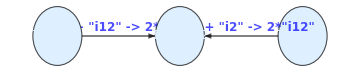

```mathematica
(*part. case*)RNbg={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"+"i12"->2*"i12","i1"+"i12"->2*"i12","i2"+"i12"->2*"i12","s"->0,"i1"->0,"i2"->0,"i12"->0};
rtsbg={s0 mu0,mu1 s0^(-1)  *R1*s*i1,mu2  s0^(-1)  *R2*s*i2,mu3  s0^(-1)  *R3*s*i12,et1*i1*i12,et2*i2*i12,mu0*s,mu1*i1,mu2*i2,mu3*i12};
Print[RNbg//Length,"reactions and transitions: ",Transpose[{RNbg,rtsbg}]//MatrixForm]
{RHS,var,par,cp,mSi,Jx,Jy,cDFE,E0,K,R0A,infVars,ng}= NGMRN[RNbg,rtsbg,var];
Print["RHS=",RHS//FullSimplify//MatrixForm,"mSi=",mSi];

F=ng[[2]];V=ng[[3]];
Print["al,be are",al//MatrixForm,be//MatrixForm,"  DFE is",E0," repr. functions  ",R0A];
Print["K=",K//MatrixForm,"F=",F//MatrixForm,"V=",V//MatrixForm];
{edg,elab,cyc,graph}=IGMS[RNbg, mSi];
```

```mathematica
s1=1/R1;
s2=1/R2;s3=1/R3;s13=s0/(1+mu1 mu3 (1/s1-1/s3)/(et1  mu0));
s23=s0/(1+mu2 mu3 (1/s2-1/s3)/(et2 mu0));con=And@@cp&&s0>s3>s23>s2&&s3>s13>s1;
fi=FindInstance[con,par][[1]]
```

{et1→5/8,et2→5/8,mu0→1,mu1→1,mu2→1,mu3→1,R1→2,R2→2,R3→1,s0→2}

```mathematica
(*Siphon face i1=0*)
RHSc1=RHS/.c1;
cN=Join[cmu,cbg,(cb/.cmu),fi];
Print["Using FULL 3D system (s,i2,i12) on i1=0 face"];
{Xs1,eig1,stab1,sad1,pFP1,pStr1,rhN1}=phase2[RHSc1[[{1,3,4}]],{s,i2,i12},cN];
Print["Face i1=0: Xs=",Xs1," stab=",stab1]
```

Using FULL 3D system (s,i2,i12) on i1=0 face

dyn aft sub={2 mu-mu s-(i12 mu s)/2-i2 mu s,-(5 i12 i2)/8-i2 mu+i2 mu s,(5 i12 i2)/8-i12 mu+(i12 mu s)/2}

Eigenvalues::matsq: Argument {{0.,0.,-109.586,0.},{-5.19832,0.,91.2921,0.},{5.19832,0.,0.,0.}} at position 1 is not a non-empty square matrix.

fp={{0.,8.3173,0.,11.9762}} eig={Eigenvalues[{{0.,0.,-109.586,0.},{-5.19832,0.,91.2921,0.},{5.19832,0.,0.,0.}}]} stab={Which[Eigenvalues[{{0.,0.,-109.586,0.},{-5.19832,0.,91.2921,0.},{5.19832,0.,0.,0.}}]<0,Stable,AllTrue[Re[EpidCRN`Private`eigVals$245110⟦EpidCRN`Private`i⟧],#1>0&],Unstable,True,Saddle]}

Face i1=0: Xs={{0.,8.3173,0.,11.9762}} stab={Which[Eigenvalues[{{0.,0.,-109.586,0.},{-5.19832,0.,91.2921,0.},{5.19832,0.,0.,0.}}]<0,Stable,AllTrue[Re[EpidCRN`Private`eigVals$245110⟦EpidCRN`Private`i⟧],#1>0&],Unstable,True,Saddle]}

dyn aft sub={0.05 i_2-0.1 i_12 i_2,0.02 i_12+0.1 i_12 i_2}

fp={{0.,0.}} eig={{-0.0316228,0.0316228}} stab={Saddle}

Face i1=0: Xs={{0.,0.}} stab={Saddle}

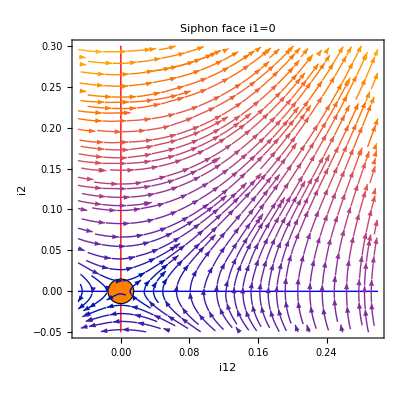

```mathematica
Show[pFP1,pStr1,PlotLabel->"Siphon face i1=0"]
(*phN[rhN1]*)
```

dyn aft sub={0.05 i_1-0.05 i_1 i_12,0.02 i_12+0.05 i_1 i_12}

fp={{0.,0.}} eig={{0.05,0.02}} stab={Unstable}

Face i2=0: Xs={{0.,0.}} stab={Unstable}

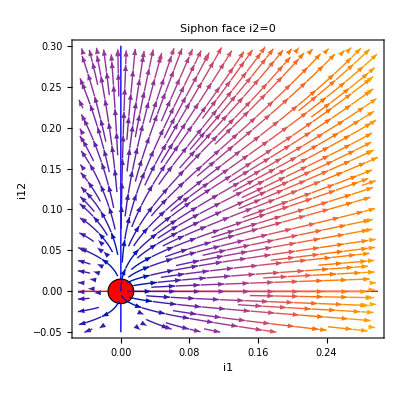

dyn aft sub={0.05 i_1,0.02 i_2}

fp={{0,0}} eig={{0.05,0.02}} stab={Unstable}

Face i12=0: Xs={{0,0}} stab={Unstable}

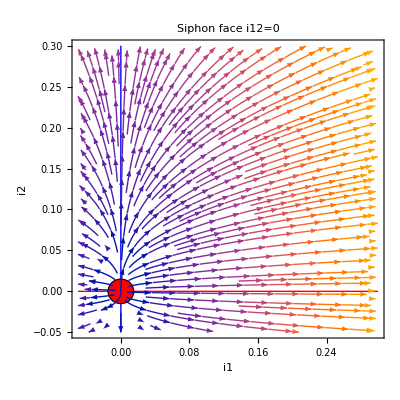

```mathematica
(*Siphon face i2=0*)
RHSc2=RHS/.c2;
{Xs2,eig2,stab2,sad2,pFP2,pStr2,rhN2}=phase2[RHSc2[[{2,4}]],{i1,i12},Join[cmu,cbe,(cb/.cmu),{s->1,s0->1,mu->0.1,et1->0.05,et2->0,R1->1.5,R3->1.2}]];
Print["Face i2=0: Xs=",Xs2," stab=",stab2]
Show[pFP2,pStr2,PlotLabel->"Siphon face i2=0"]
(*Siphon face i12=0*)
RHSc3=RHS/.c3;
{Xs3,eig3,stab3,sad3,pFP3,pStr3,rhN3}=phase2[RHSc3[[{2,3}]],{i1,i2},Join[cmu,cbe,(cb/.cmu),{s->1,s0->1,mu->0.1,et1->0.05,et2->0.05,R1->1.5,R2->1.2}]];
Print["Face i12=0: Xs=",Xs3," stab=",stab3]
Show[pFP3,pStr3,PlotLabel->"Siphon face i12=0"]
```

```mathematica
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infV,gam,Et}=bdCom[RNbg, rtsbg];
Print["The ", Et//Length ," Et elts have  3,3,2 coms "];
Print["Et1= ",Et1=Et[[1]],"Et2= ",
Et2=Et[[2]],"Et3= ",
Et3=Et[[3]]];
eq=Thread[(RHS/.cbg/.c2)==0];
so=Solve[eq,var]//FullSimplify;(*4 solutions*)
Print["the",so//Length,"sols on siphon 2 are",so];
jac=Grad[RHS,var];
```

Set::shape: Lists {RHS,var,par,cp,mSi,Jx,Jy,E0,K,R0A,«3»} and bdCom[{0→s,i1+s→2 i1,i2+s→2 i2,i12+s→2 i12,i1+i12→2 i12,i12+i2→2 i12,s→0,i1→0,i2→0,i12→0},{μ_0 s_0,(i_1 μ_1 R_1 s)/s_0,(i_2 μ_2 R_2 s)/s_0,(i_12 μ_3 R_3 s)/s_0,η_1 i_1 i_12,η_2 i_12 i_2,μ_0 s,i_1 μ_1,i_2 μ_2,i_12 μ_3}] are not the same shape.

The 0 Et elts have  3,3,2 coms

Part::partd: Part specification Et⟦1⟧ is longer than depth of object.

Part::partd: Part specification Et⟦2⟧ is longer than depth of object.

Part::partd: Part specification Et⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Et1= Et⟦1⟧Et2= Et⟦2⟧Et3= Et⟦3⟧

Solve::svars: Equations may not give solutions for all "solve" variables.

the4sols on siphon 2 are{{s→s_0,i_1→0,i_12→0},{s→s_0/R_1,i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_12→0},{s→s_0/R_3,i_1→0,i_12→(μ_0 (-1+R_3) s_0)/(μ_3 R_3)},{s→(η_1 μ_0 s_0^2)/(μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0),i_1→(μ_3 (μ_1 μ_3 (R_1-R_3)-η_1 μ_0 (-1+R_3) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0)),i_12→(μ_1 (μ_1 μ_3 (-R_1+R_3)+η_1 μ_0 (-1+R_1) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0))}}

```mathematica
(*all fps*)
eq=Thread[RHS==0];so=Solve[eq,var];(*7 solutions*)
Print[so//Length," sols"]
so//FullSimplify
cD=so[[1]];cE1=so[[2]];cE2=so[[3]];cE3=so[[5]];cEE=so[[4]];c13=so[[6]];
Print["s13= ",s13=s/.c13//FullSimplify]
i131=i1/.c13; i131-mu3(1-R3 s13/s0) /et1//FullSimplify
i133=i12/.c13//FullSimplify;
i133-(R1 s13/s0 -1)mu1/et1//FullSimplify
c23=so[[7]];
con=Join[cp,Thread[Drop[var/.cE1,{3,4}]>0]];
jEE=jac/.cEE//FullSimplify;
(*Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[jEE,u]]]//Factor*)
EE=var/.cEE;
ine=Join[Thread[EE>0],cp,{et1 mu2>et2 mu1,R2<R1<R2 et1 mu2/et2 mu1}]
ret=Reduce[ine/.cmu];re=FullSimplify[ret,cp]
(*{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
ll//Length
ql//Length
hDeg*)

(*con=Join[cp,Thread[Drop[var/.c13,3]>0]];
Print["E13 exists if"]
re11=reCL[Reduce[con]//Factor]*)
```

7 sols

{{s→s_0,i_1→0,i_2→0,i_12→0},{s→s_0/R_1,i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_2→0,i_12→0},{s→s_0/R_2,i_1→0,i_2→(μ_0 (-1+R_2) s_0)/(μ_2 R_2),i_12→0},{s→((η_2 μ_1-η_1 μ_2) s_0)/(η_2 μ_1 R_1-η_1 μ_2 R_2),i_1→(μ_2 (-η_2 μ_1+η_1 μ_2) μ_3 (R_2-R_3)+η_2 μ_0 (η_2 μ_1 (-1+R_1)-η_1 μ_2 (-1+R_2)) s_0)/((η_2 μ_1-η_1 μ_2) (η_2 μ_1 R_1-η_1 μ_2 R_2)),i_2→(μ_1 (η_2 μ_1-η_1 μ_2) μ_3 (R_1-R_3)+η_1 μ_0 (η_2 (μ_1-μ_1 R_1)+η_1 μ_2 (-1+R_2)) s_0)/((η_2 μ_1-η_1 μ_2) (η_2 μ_1 R_1-η_1 μ_2 R_2)),i_12→(μ_1 μ_2 (-R_1+R_2))/(η_2 μ_1 R_1-η_1 μ_2 R_2)},{s→s_0/R_3,i_1→0,i_2→0,i_12→(μ_0 (-1+R_3) s_0)/(μ_3 R_3)},{s→(η_1 μ_0 s_0^2)/(μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0),i_1→(μ_3 (μ_1 μ_3 (R_1-R_3)-η_1 μ_0 (-1+R_3) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0)),i_2→0,i_12→(μ_1 (μ_1 μ_3 (-R_1+R_3)+η_1 μ_0 (-1+R_1) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0))},{s→(η_2 μ_0 s_0^2)/(μ_2 μ_3 (R_2-R_3)+η_2 μ_0 s_0),i_1→0,i_2→(μ_3 (μ_2 μ_3 (R_2-R_3)-η_2 μ_0 (-1+R_3) s_0))/(η_2 (μ_2 μ_3 (R_2-R_3)+η_2 μ_0 s_0)),i_12→(μ_2 (μ_2 μ_3 (-R_2+R_3)+η_2 μ_0 (-1+R_2) s_0))/(η_2 (μ_2 μ_3 (R_2-R_3)+η_2 μ_0 s_0))}}

s13= (η_1 μ_0 s_0^2)/(μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0)

0

0

{((η_2 μ_1-η_1 μ_2) s_0)/(η_2 μ_1 R_1-η_1 μ_2 R_2)>0,(-η_2 μ_1 μ_2 μ_3 R_2+η_1 μ_2^2 μ_3 R_2+η_2 μ_1 μ_2 μ_3 R_3-η_1 μ_2^2 μ_3 R_3-η_2^2 μ_0 μ_1 s_0+η_1 η_2 μ_0 μ_2 s_0+η_2^2 μ_0 μ_1 R_1 s_0-η_1 η_2 μ_0 μ_2 R_2 s_0)/((η_2 μ_1-η_1 μ_2) (η_2 μ_1 R_1-η_1 μ_2 R_2))>0,(η_2 μ_1^2 μ_3 R_1-η_1 μ_1 μ_2 μ_3 R_1-η_2 μ_1^2 μ_3 R_3+η_1 μ_1 μ_2 μ_3 R_3+η_1 η_2 μ_0 μ_1 s_0-η_1^2 μ_0 μ_2 s_0-η_1 η_2 μ_0 μ_1 R_1 s_0+η_1^2 μ_0 μ_2 R_2 s_0)/((η_2 μ_1-η_1 μ_2) (η_2 μ_1 R_1-η_1 μ_2 R_2))>0,-(μ_1 μ_2 (R_1-R_2))/(η_2 μ_1 R_1-η_1 μ_2 R_2)>0,η_1>0,η_2>0,μ_0>0,μ_1>0,μ_2>0,μ_3>0,R_1>0,R_2>0,R_3>0,s_0>0,η_1 μ_2>η_2 μ_1,R_2<R_1<(η_1 μ_1 μ_2 R_2)/η_2}

R_2>1&&R_1>R_2&&η_1>(η_2 (-1+R_1))/(-1+R_2)&&R_3<(-η_2 R_1+η_1 R_2)/(η_1-η_2)&&μ>√((η_2 R_1)/(η_1 R_2))&&((η_1-η_2) μ (R_1-R_3))/(η_1 (η_2-η_2 R_1+η_1 (-1+R_2)))<s_0<-((η_1-η_2) μ (R_2-R_3))/(η_2 (η_1+η_2 (-1+R_1)-η_1 R_2))

```mathematica
re
```

R_1>1&&R_3<(η_2 μ_1 R_1-η_1 μ_2 R_2)/(η_2 μ_1-η_1 μ_2)&&(μ_1 (-η_2 μ_1+η_1 μ_2) μ_3 (R_1-R_3))/(η_1 (η_2 (μ_1-μ_1 R_1)+η_1 μ_2 (-1+R_2)) s_0)<μ_0<(μ_2 (η_2 μ_1-η_1 μ_2) μ_3 (R_2-R_3))/(η_2 (η_2 μ_1 (-1+R_1)-η_1 μ_2 (-1+R_2)) s_0)&&((R_2>1&&(μ_1≥1||R_2≤R_1/(-μ_1^2 (-1+R_1)+R_1))&&(μ_1<1||R_2<R_1)&&η_1>(η_2 μ_1 (-1+R_1))/(μ_2 (-1+R_2)))||(η_1 μ_1 μ_2 R_2>η_2 R_1&&R_1/(-μ_1^2 (-1+R_1)+R_1)<R_2<R_1&&μ_1<1))

```mathematica
(*Stab E1*)
j1=jac/.cE1//FullSimplify;j1//MatrixForm
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
```

```mathematica
lSta
qSta
Print["E1 stable if R1(s13) >1"]
re=reCL[Reduce[Join[cp,lSta,qSta]]//FullSimplify]//FullSimplify
cpL=And@@Drop[cp,-1]&&R1>1;
re1=FullSimplify[re,cpL]
```

{μ_2 R_1-μ_2 R_2>0,μ_1 μ_3 R_1-μ_1 μ_3 R_3+μ_0 s_0 η_1-μ_0 R_1 s_0 η_1>0}

{μ_0 R_1>0,-μ_0 μ_1+μ_0 μ_1 R_1>0}

E1 stable if R1(s13) >1

(R_1>R_3&&R_3>1&&μ_0<(μ_1 μ_3 (R_1-R_3))/((-1+R_1) s_0 η_1)&&R_2<R_1)||(R_1>1&&R_1>R_2&&μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_1) s_0 η_1<0&&R_3≤1)

μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_1) s_0 η_1<0&&R_1>R_2&&(R_1>R_3||R_3≤1)

```mathematica
(*Stab E3*)j3=jac/.cE3//FullSimplify;j3//MatrixForm
Print[" At cE3, chp of jac, ch3, factorizes as"]
ch3=Numerator[Together[CharacteristicPolynomial[j3,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch3,par];
ll//Length
ql//Length
hDeg

ret=Reduce[Join[cp,lSta,qSta,{R3>1(*,R1>R2*)}]]//FullSimplify;
cond=And@@cp&&R3>1
Print["E3 stable if R1(s11) <1"]
re3=FullSimplify[ret,cond]
re3//Length
re31=re3[[1]]
re31//Length
re32=re3[[2]];re=BooleanMinimize[LogicalExpand[re3]]//FullSimplify
FullSimplify[re3,cond]
FullSimplify[re,cond]
lo=LogicalExpand[re]
Resolve[lo,Reals]
```

(-μ_0 R_3 | -(μ_1 R_1)/R_3 | -(μ_2 R_2)/R_3 | -μ_3
0 | (μ_1 μ_3 (R_1-R_3)-μ_0 (-1+R_3) s_0 η_1)/(μ_3 R_3) | 0 | 0
0 | 0 | (μ_2 μ_3 (R_2-R_3)-μ_0 (-1+R_3) s_0 η_2)/(μ_3 R_3) | 0
μ_0 (-1+R_3) | (μ_0 (-1+R_3) s_0 η_1)/(μ_3 R_3) | (μ_0 (-1+R_3) s_0 η_2)/(μ_3 R_3) | 0)

At cE3, chp of jac, ch3, factorizes as

(-μ_0 μ_3+μ_0 μ_3 R_3+μ_0 R_3 u+u^2) (-μ_1 μ_3 R_1+μ_1 μ_3 R_3+μ_3 R_3 u-μ_0 s_0 η_1+μ_0 R_3 s_0 η_1) (-μ_2 μ_3 R_2+μ_2 μ_3 R_3+μ_3 R_3 u-μ_0 s_0 η_2+μ_0 R_3 s_0 η_2)

2

1

{}

μ_0>0&&μ_1>0&&μ_2>0&&μ_3>0&&R_1>0&&R_2>0&&R_3>0&&s_0>0&&η_1>0&&η_2>0&&R_3>1

E3 stable if R1(s11) <1

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

2

R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0

2

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤1)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤R_3)||(μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0&&R_1≤R_3)||(R_1≤R_3&&R_2≤1)||(R_1≤R_3&&R_2≤R_3)

(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤1)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤R_3)||(μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0&&R_1≤R_3)||(R_1≤R_3&&R_2≤1)||(R_1≤R_3&&R_2≤R_3)

```mathematica
(*Stab E13*)
j13=jac/.c13//FullSimplify;
Print[" At cE13, chp of jac factorizes as"]
ch13=Numerator[Together[CharacteristicPolynomial[j13,u]]]//Factor
ch13//Length
co2=CoefficientList[ch13[[2]],u]//FullSimplify
```

At cE13, chp of jac factorizes as

(μ_1^4 μ_3^4 R_1^3-3 μ_1^4 μ_3^4 R_1^2 R_3+3 μ_1^4 μ_3^4 R_1 R_3^2-μ_1^4 μ_3^4 R_3^3-μ_1^3 μ_3^3 R_1^3 u^2+3 μ_1^3 μ_3^3 R_1^2 R_3 u^2-3 μ_1^3 μ_3^3 R_1 R_3^2 u^2+μ_1^3 μ_3^3 R_3^3 u^2+3 μ_0 μ_1^3 μ_3^3 R_1^2 s_0 η_1-μ_0 μ_1^3 μ_3^3 R_1^3 s_0 η_1-6 μ_0 μ_1^3 μ_3^3 R_1 R_3 s_0 η_1+μ_0 μ_1^3 μ_3^3 R_1^2 R_3 s_0 η_1+3 μ_0 μ_1^3 μ_3^3 R_3^2 s_0 η_1+μ_0 μ_1^3 μ_3^3 R_1 R_3^2 s_0 η_1-μ_0 μ_1^3 μ_3^3 R_3^3 s_0 η_1+μ_1^3 μ_3^3 R_1^2 s_0 u η_1-μ_0 μ_1^3 μ_3^2 R_1^3 s_0 u η_1-2 μ_1^3 μ_3^3 R_1 R_3 s_0 u η_1+μ_0 μ_1^3 μ_3^2 R_1^2 R_3 s_0 u η_1+μ_1^3 μ_3^3 R_3^2 s_0 u η_1+μ_0 μ_1^2 μ_3^3 R_1 R_3^2 s_0 u η_1-μ_0 μ_1^2 μ_3^3 R_3^3 s_0 u η_1-3 μ_0 μ_1^2 μ_3^2 R_1^2 s_0 u^2 η_1+6 μ_0 μ_1^2 μ_3^2 R_1 R_3 s_0 u^2 η_1-3 μ_0 μ_1^2 μ_3^2 R_3^2 s_0 u^2 η_1-μ_1^2 μ_3^2 R_1^2 s_0 u^3 η_1+2 μ_1^2 μ_3^2 R_1 R_3 s_0 u^3 η_1-μ_1^2 μ_3^2 R_3^2 s_0 u^3 η_1+3 μ_0^2 μ_1^2 μ_3^2 R_1 s_0^2 η_1^2-2 μ_0^2 μ_1^2 μ_3^2 R_1^2 s_0^2 η_1^2-3 μ_0^2 μ_1^2 μ_3^2 R_3 s_0^2 η_1^2+μ_0^2 μ_1^2 μ_3^2 R_1^2 R_3 s_0^2 η_1^2+2 μ_0^2 μ_1^2 μ_3^2 R_3^2 s_0^2 η_1^2-μ_0^2 μ_1^2 μ_3^2 R_1 R_3^2 s_0^2 η_1^2+2 μ_0 μ_1^2 μ_3^2 R_1 s_0^2 u η_1^2-μ_0^2 μ_1^2 μ_3 R_1^2 s_0^2 u η_1^2-μ_0 μ_1^2 μ_3^2 R_1^2 s_0^2 u η_1^2-2 μ_0 μ_1^2 μ_3^2 R_3 s_0^2 u η_1^2+μ_0^2 μ_1^2 μ_3 R_1^2 R_3 s_0^2 u η_1^2+μ_0^2 μ_1 μ_3^2 R_3^2 s_0^2 u η_1^2+μ_0 μ_1^2 μ_3^2 R_3^2 s_0^2 u η_1^2-μ_0^2 μ_1 μ_3^2 R_1 R_3^2 s_0^2 u η_1^2-3 μ_0^2 μ_1 μ_3 R_1 s_0^2 u^2 η_1^2+3 μ_0^2 μ_1 μ_3 R_3 s_0^2 u^2 η_1^2-2 μ_0 μ_1 μ_3 R_1 s_0^2 u^3 η_1^2+2 μ_0 μ_1 μ_3 R_3 s_0^2 u^3 η_1^2+μ_0^3 μ_1 μ_3 s_0^3 η_1^3-μ_0^3 μ_1 μ_3 R_1 s_0^3 η_1^3-μ_0^3 μ_1 μ_3 R_3 s_0^3 η_1^3+μ_0^3 μ_1 μ_3 R_1 R_3 s_0^3 η_1^3+μ_0^2 μ_1 μ_3 s_0^3 u η_1^3-μ_0^2 μ_1 μ_3 R_1 s_0^3 u η_1^3-μ_0^2 μ_1 μ_3 R_3 s_0^3 u η_1^3+μ_0^2 μ_1 μ_3 R_1 R_3 s_0^3 u η_1^3-μ_0^3 s_0^3 u^2 η_1^3-μ_0^2 s_0^3 u^3 η_1^3) (-μ_1 μ_2 μ_3 R_1 η_1+μ_1 μ_2 μ_3 R_3 η_1-μ_1 μ_3 R_1 u η_1+μ_1 μ_3 R_3 u η_1-μ_0 μ_2 s_0 η_1^2+μ_0 μ_2 R_2 s_0 η_1^2-μ_0 s_0 u η_1^2+μ_1^2 μ_3 R_1 η_2-μ_1^2 μ_3 R_3 η_2+μ_0 μ_1 s_0 η_1 η_2-μ_0 μ_1 R_1 s_0 η_1 η_2)

2

{μ_0 μ_2 (-1+R_2) s_0 η_1^2+μ_1^2 μ_3 (R_1-R_3) η_2+μ_1 η_1 (μ_2 μ_3 (-R_1+R_3)-μ_0 (-1+R_1) s_0 η_2),-η_1 (μ_1 μ_3 (R_1-R_3)+μ_0 s_0 η_1)}

```mathematica
v23=Drop[var/.c23//FullSimplify,{2}];
(*Print["E23 exists if"]*)
re2=reCL[Factor/@Reduce[Join[cp,Thread[v23>0]]]];
Print["EE exists if"]
reE=reCL[Factor/@Reduce[Join[cp,Thread[(var/.cEE)>0],{R1>R2}]]]
reE[[2,1]]
```

EE exists if

R_2>1&&R_1>R_2&&0<μ_1<(μ_2 (-1+R_2) η_1)/((-1+R_1) η_2)&&0<R_3<(μ_2 R_2 η_1-μ_1 R_1 η_2)/(μ_2 η_1-μ_1 η_2)&&(μ_1 μ_3 (R_1-R_3) (-μ_2 η_1+μ_1 η_2))/(s_0 η_1 (μ_2 η_1-μ_2 R_2 η_1-μ_1 η_2+μ_1 R_1 η_2))<μ_0<(μ_2 μ_3 (R_2-R_3) (μ_2 η_1-μ_1 η_2))/(s_0 η_2 (-μ_2 η_1+μ_2 R_2 η_1+μ_1 η_2-μ_1 R_1 η_2))

```mathematica
cpl=And@@cp;
fi=FindInstance[reE&&re1&&re2&&cpl&&R1>1&&R2>1&&R3>1,par]
```

{{μ_0→5/4,μ_1→3/2,μ_2→1,μ_3→1,R_1→39/32,R_2→5/4,R_3→17/16,s_0→1,η_1→1,η_2→1}}

```mathematica
Timing[re=reCL[Reduce[reE&&re1&&re2&&cpl&&R1>1&&R2>1&&R3>1]//FullSimplify]]
```

$Aborted

```mathematica
cN={be1->0.5,be2->0.4,mu0->0.1,mu1->0.2,mu2->0.2,mu3->0.3,R2->1.5,R3->2.0,et1->0.3,et2->0.3,ga1->0.2,ga2->0.2,s0->100};
res1=invGr[mSi,{},R0A/.cN/.{R1->0.8},RHS,var,E0/.cN/.{R1->0.8}];
res2=invGr[mSi,{},R0A/.cN/.{R1->1.5},RHS,var,E0/.cN/.{R1->1.5}];
res3=invGr[mSi,{},R0A/.cN/.{R1->1.6},RHS,var,E0/.cN/.{R1->1.6}];
res4=invGr[mSi,{},R0A/.cN/.{R1->2.0},RHS,var,E0/.cN/.{R1->2.0}];
GraphicsRow[{res1[[1]],res3[[1]],res4[[1]]},Spacings->20]
```